## Reduction alg, high precision

This computes the reduced nodes/weights in extended precision, using 60 digits

```mathematica
formMatrixForReductionHalfLine[r_,b_]:=
 Outer[Times,Conjugate[Sqrt[b]],Sqrt[b]]* Outer[1/(#1+ #2)&,Conjugate[r],r]
```

```mathematica
computeConEigenvalue[mat_,tol_]:=Module[{matForReduction,eigenValues,eigenVectors,smallEigenvalueIndex,v,error},
matForReduction = Conjugate[mat] . mat;
{eigenValues,eigenVectors} = Eigensystem[matForReduction ];
smallEigenvalueIndex= Position[(#<tol)&/@Sqrt[Abs[eigenValues]],True,1,1]//Flatten//First;
v = eigenVectors[[smallEigenvalueIndex]];
error = matForReduction . v-eigenValues[[smallEigenvalueIndex]]v//Abs//Max;
{error,v,eigenValues,smallEigenvalueIndex}]
```

```mathematica
findRootsRationalFuncHalfLine[gamma0_,w0_,v_]:=Module[{r1,b1,v1,w,x,f,a,delta,b,A,eigs,roots,rationalFunc},
w = Conjugate[Sqrt[w0]]*Conjugate[v];
x = -Conjugate[gamma0];
(*f= w/(x-z)//Total;*)
a=-w/Total[w];
delta = x;
b = x;
A=DiagonalMatrix[delta]+ Outer[Times,a,b];
eigs=Eigenvalues[A];
eigs = Select[eigs,Re[#]>10^(-32)&];
(*eigs=Delete[eigs,Position[Abs[eigs],Min[Abs[eigs]]]];*)
(*roots =z/.( SetPrecision[f,300]//Together//Numerator//NSolve[#,z]&//N);
roots=Select[roots,Abs[#]<1&]//Sort//Select[#,Abs[#]>10^-8&]&;*)
eigs]
```

```mathematica
formMatrixForWeightsHalfLine[γNew_]:=
  Outer[1/(#1+ #2)^3&,Conjugate[γNew],γNew]
```

```mathematica
formRhsForWeightsHalfLine[γ_,γNew_,w_]:=
  Outer[1/(#1+ #2)^3&,Conjugate[γNew],γ] . w
```

```mathematica
solveForWeightsHalfLine[γ_,γNew_,w_]:=Module[{matrixForWeights,rhsForWeights},
matrixForWeights=formMatrixForWeightsHalfLine[γNew];
rhsForWeights = formRhsForWeightsHalfLine[γ,γNew,w];
 LinearSolve[matrixForWeights,rhsForWeights]]
```

```mathematica
computeExpReductionHalfLine[gamma_,w_,tol_]:=Module[{wH,gammaH,matrixForReduction ,v,rationalFunc,newNodes,newWeights,dataNew,dataOld,error,eigenValues,smallEigenvalueIndex},
{wH,gammaH}={w,gamma}//SetPrecision[#,60]&;
matrixForReduction = formMatrixForReductionHalfLine[gammaH,wH];
{error,v,eigenValues,smallEigenvalueIndex} = computeConEigenvalue[matrixForReduction,tol]//SetPrecision[#,60]&;
newNodes=findRootsRationalFuncHalfLine[gammaH,wH,v];
newWeights=solveForWeightsHalfLine[gammaH,newNodes,wH];
{newNodes,newWeights}]
```

## code for sampling and using Hankel formulation for reduction

```mathematica
computeSingularValueDecomp[mat_,tol_]:=
Module[{U,V,W,singularValues,smallSingValueIndex,smallSingValue,v},
{U,W,V}= SingularValueDecomposition[mat];
singularValues =Table[W[[i,i]],{i,1,Length[W]}];
smallSingValue= Select[singularValues,Abs[#]<tol&,1];
smallSingValueIndex= Position[(#<tol)&/@singularValues,True,1,1]//Flatten//First;
v =Transpose[Conjugate[U]][[smallSingValueIndex]];
{smallSingValueIndex,smallSingValue ,v,singularValues}]
```

```mathematica
computeRootsFromEigenVec[u_]:=Module[{polynomialForRoots0,rulesForNodes0 ,nodes0,error0,accurateNodes0},
polynomialForRoots0 = u*z^(Range[Length[u]]-1)//Total;
rulesForNodes0 = NSolve[polynomialForRoots0,z];
nodes0 =(rulesForNodes0//Flatten)/.(z->stuff_)->stuff;
error0=polynomialForRoots0/.rulesForNodes0;
{error0,nodes0}]
```

```mathematica
solveForWeights[nodes_,sampledFunc_,M_]:=Module[{matrixForWeights0,V0,rhsForWeights0 },
matrixForWeights0=(1-#^(2*M+1))/(1-#)&[Outer[Times,Conjugate[nodes ],nodes]];
V0 = Map[#^Prepend[Range[2*M],0]&,nodes]//Conjugate;
rhsForWeights0 = V0 . sampledFunc;
 LinearSolve[matrixForWeights0,rhsForWeights0]]
```

```mathematica
computeExpApproximationUsingHankel[data_,tol_]:=Module[{M,hankel,v,nodesSmall,error,nodes,weights,expApproxOfData},
M = (Length[data]-1)/2;
hankel=Table[data[[i+j+1]],{i,0,M},{j,0,M}];
v=computeSingularValueDecomp[hankel,tol][[3]];
nodes=computeRootsFromEigenVec[v][[2]]//Select[#,Abs[#]<1&]&;
weights = solveForWeights[nodes,data,M]//Chop;
expApproxOfData = Array[Total[weights nodes^#]&,2*M+1,0]//Chop;
error =data-expApproxOfData;
{nodes,weights,error}]
```

```mathematica
computeExpApproximationUsingHankel[r_,b_,M_,tol_]:=Module[{data,hankel,v,nodesSmall,error,nodes,weights,expApproxOfData},
data = Table[Total[b r^(k-1)],{k,1,2*M+1}];
hankel=Table[data[[i+j+1]],{i,0,M},{j,0,M}];
v=computeSingularValueDecomp[hankel,tol][[3]];
nodes=computeRootsFromEigenVec[v][[2]]//Select[#,Abs[#]<1&]&;
weights = solveForWeights[nodes,data,M]//Chop;
expApproxOfData = Array[Total[weights nodes^#]&,2*M+1,0]//Chop;
error =data-expApproxOfData//Abs//Max;
{nodes,weights,error}]
```

```mathematica
LInfinitySolve[A_,b_]:=Module[{m,n,Aall,ball,c,x,bds,onesT},
{m,n}=Dimensions[A];
onesT = {Table[1,{m}]};
Aall = Join[Transpose[Join[onesT,Transpose[-A]]], Transpose[Join[onesT,Transpose[A]]]];
ball = Join[-b,b];
c = Join[{1},Table[0,{n}]];
bds = Table[{-Infinity,Infinity},{n+1}];
x = LinearProgramming[c,Aall,ball,bds];
Take[x,-n]
]
```

```mathematica
interpAtom[d_,n_,x_]:= SetPrecision[LaguerreL[n,1/2,SetPrecision[x,60]^2] 1/Sqrt[SetPrecision[Pi,60] d]Exp[-x^2/d],60]
```

## Computation of Gaussian approximation of (ⅇ^(-x^2/4))/(2 √π) in the paper

Compute (near) optional rational approximation of the Gaussian (ⅇ^(-x^2/4))/(2 √π); note that there is an additional step to get the imaginary part of the poles to be aligned with the integers

```mathematica
d0 = 4;
```

```mathematica
gaussian = interpAtom[d0,0,x]
```

0.282094791773878143474039725780386292922025314664499428422043 2.71828182845904523536028747135266249775724709369995957496697^(-0.25 x^2)

```mathematica
gaussianFT = Integrate[gaussian Exp[I k x],{x,-Infinity,Infinity}];
Precision[gaussianFT]
```

0.

```mathematica
M = 100;
R = 10;
pts = SetPrecision[R Range[0,2*M-1]/(2 M),60];
fVals = SetPrecision[gaussianFT/.k->pts,120];
(*THIS IS THE PART WHERE WE SET THE TOLERANCE, SMALLER TOLERANCE REQUIRES MORE POLES*)
tol = 10^-22;
{nodes,weights,error} = computeExpApproximationUsingHankel[fVals,tol];
alphasAtom =  2 M Log[nodes]/R//Conjugate;
weightsAtom = -(1/SetPrecision[Pi,60]) weights//Conjugate;
Precision[tol]
```

∞

Plot the error in the rational approximation of the Gaussian (ⅇ^(-x^2/4))/(2 √π)

weights

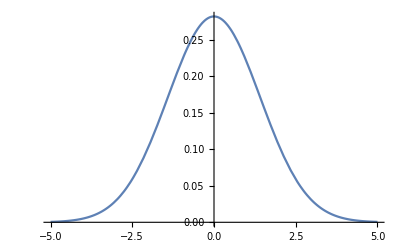

```mathematica
rationalFuncExpr = Total[weightsAtom/(I SetPrecision[x,60] + alphasAtom)]//Re;
Plot[rationalFuncExpr,{x,-5,5},PlotRange->All]
```

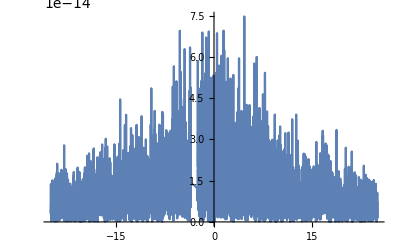

```mathematica
rationalFuncExpr = Total[weightsAtom/(I  SetPrecision[x,60] + alphasAtom)]//Re;
plotRationalApproxGaussianOpt=Plot[rationalFuncExpr-gaussian//Abs,{x,-25,25},PlotRange->All]
```

Now, construct the rational approximation of rational approximation of the Gaussian (ⅇ^(-x^2/4))/(2 √π) where the imaginary part of the poles are integers

```mathematica
alphaReMin = alphasAtom//Re//Abs//Min;
alphaReMax = alphasAtom//Re//Abs//Max;
alphaReAv = (alphaReMin+alphaReMax)/2;
```

```mathematica
alphasAtom//Length
```

15

```mathematica
Precision[alphaReMin]
```

113.739

Redefining poles, finding residues through convex optimization

```mathematica
gamma= -alphaReMin+I Range[-22,22];
```

```mathematica
N1 = 800;
xPts1 = 60 Range[-N1,N1]/(2N1);
N2 = 60;
xPts2 = 90 Range[0,N2]/N2 + 15;
xPts3 = -Reverse[xPts2];
xPts = Join[xPts3,xPts1,xPts2];
tau = Re[gamma];
theta = Im[gamma];
```

```mathematica
b = gaussian/.x->xPts//SetPrecision[#,120]&;
Precision[b]
A = ConstantArray[0,{Length[xPts],2*Length[tau]}];
Precision[A]
A[[1;;Length[xPts],1;;Length[tau]]] = Table[( xPts[[i]] - theta[[j]])/((xPts[[i]] - theta[[j]])^2+tau[[j]]^2),{i,1,Length[xPts]},{j,1,Length[tau]}];
A[[1;;Length[xPts],Length[tau]+1;;2*Length[tau]]] = Table[- tau[[j]]/((xPts[[i]] - theta[[j]])^2+tau[[j]]^2),{i,1,Length[xPts]},{j,1,Length[tau]}];
```

116.559

∞

```mathematica
A=SetPrecision[A,11];
b=SetPrecision[b,11];
w1 = LInfinitySolve[A,b];
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

Take::take: Cannot take positions -90 through -1 in LinearProgramming[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«41»},{«1»},«1»,{{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},«29»,{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},{-∞,∞},«41»}].

Here a are residues corresponding to new poles

```mathematica
a = w1[[Length[w1]/2+1;;Length[w1]]]+I w1[[1;;Length[w1]/2]];
a = -a;
```

```mathematica
a
Precision[a]
```

90-ⅈ LinearProgramming[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1},1,{{-∞,∞},{-∞,∞},88,{-∞,∞}}]
 |  |  |  |

11.

### Finally, here is the final rational approximation of (ⅇ^(-x^2/4))/(2 √π)

```mathematica
gamma;
ScientificForm[%,30]
```

{-4.62434339499671423814277334911-22 ⅈ,-4.62434339499671423814277334911-21 ⅈ,-4.62434339499671423814277334911-20 ⅈ,-4.62434339499671423814277334911-19 ⅈ,-4.62434339499671423814277334911-18 ⅈ,-4.62434339499671423814277334911-17 ⅈ,-4.62434339499671423814277334911-16 ⅈ,-4.62434339499671423814277334911-15 ⅈ,-4.62434339499671423814277334911-14 ⅈ,-4.62434339499671423814277334911-13 ⅈ,-4.62434339499671423814277334911-12 ⅈ,-4.62434339499671423814277334911-11 ⅈ,-4.62434339499671423814277334911-10 ⅈ,-4.62434339499671423814277334911-9 ⅈ,-4.62434339499671423814277334911-8 ⅈ,-4.62434339499671423814277334911-7 ⅈ,-4.62434339499671423814277334911-6 ⅈ,-4.62434339499671423814277334911-5 ⅈ,-4.62434339499671423814277334911-4 ⅈ,-4.62434339499671423814277334911-3 ⅈ,-4.62434339499671423814277334911-2 ⅈ,-4.62434339499671423814277334911-ⅈ,-4.62434339499671423814277334911,-4.62434339499671423814277334911+ⅈ,-4.62434339499671423814277334911+2 ⅈ,-4.62434339499671423814277334911+3 ⅈ,-4.62434339499671423814277334911+4 ⅈ,-4.62434339499671423814277334911+5 ⅈ,-4.62434339499671423814277334911+6 ⅈ,-4.62434339499671423814277334911+7 ⅈ,-4.62434339499671423814277334911+8 ⅈ,-4.62434339499671423814277334911+9 ⅈ,-4.62434339499671423814277334911+10 ⅈ,-4.62434339499671423814277334911+11 ⅈ,-4.62434339499671423814277334911+12 ⅈ,-4.62434339499671423814277334911+13 ⅈ,-4.62434339499671423814277334911+14 ⅈ,-4.62434339499671423814277334911+15 ⅈ,-4.62434339499671423814277334911+16 ⅈ,-4.62434339499671423814277334911+17 ⅈ,-4.62434339499671423814277334911+18 ⅈ,-4.62434339499671423814277334911+19 ⅈ,-4.62434339499671423814277334911+20 ⅈ,-4.62434339499671423814277334911+21 ⅈ,-4.62434339499671423814277334911+22 ⅈ}

```mathematica
a;
ScientificForm[%,30]
```

90-ⅈ LinearProgramming[1]
 |  |  |  |

```mathematica
rationalFuncExpr = Re[ Total[a/(I x + gamma)] ];
plotRationalApproxGaussianSubOpt=Plot[rationalFuncExpr-gaussian//Abs,{x,-204,204},PlotRange->All]
```

$Aborted

## Constructing rational approximations of cos(x) and sin(x)

### Getting the Gaussian approximation of cos(x) and sin(x)

```mathematica
gaussianFT = Integrate[Exp[2 Pi I x  k]Exp[-x^2/(d h^2)]/Sqrt[d Pi],{x,-Infinity,Infinity},Assumptions->d>0&&h>0];
normalization[h0_,d0_]:=
gaussianFT/.k->1/.d->d0/.h->h0//N
```

```mathematica
funcExp[x_,d_,N1_,h_]:= 1/Sqrt[d Pi]h/normalization[h,d]Sum[Exp[-2 Pi h n I] Exp[-(x+n h)^2/(d h^2)],{n,-N1,N1}]
```

```mathematica
funcCos[x_,d_,N1_,h_]:= 1/Sqrt[d Pi]h/normalization[h,d]Sum[Cos[2 Pi h n] Exp[-(x+n h)^2/(d h^2)],{n,-N1,N1}]
```

```mathematica
funcSin[x_,d_,N1_,h_]:= 1/Sqrt[d Pi] h/normalization[h,d]Sum[Sin[-2 Pi h n] Exp[-(x+n h)^2/(d h^2)],{n,-N1,N1}]
```

```mathematica
h0 = 1/10;
M = 320;
d0 = 4;
plotExpErrorGaussian=Plot[Exp[2 Pi x I]-funcExp[x,d0,M,h0]//Abs,{x,-14,14},PlotRange->All]
```

$Aborted

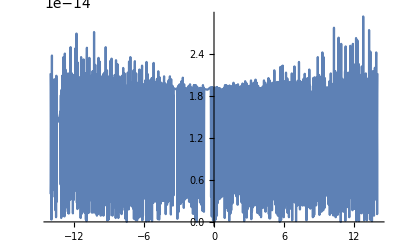

```mathematica
plotExpErrorGaussian=Plot[Cos[2 Pi x]-funcCos[x,d0,M,h0]//Abs,{x,-14,14},PlotRange->All]
```

```mathematica
plotExpErrorGaussian=Plot[Sin[2 Pi x]-funcSin[x,d0,M,h0]//Abs,{x,-14,14},PlotRange->All]
```

$Aborted

### Constructing final rational approximation

```mathematica
computeResidues[p_,func_,M_,L_,h_,aGauss_]:=Module[{L1,L2,c,ind,res},
L1 = Max[-L,p-M];
L2 = Min[L,p+M];
ind = Range[L1,L2];
c = Map[func[h #]&, p - ind];
res = Total[h aGauss[[L+ind+1]] * c];
res
]
```

Construction for sin(2 pi x)

```mathematica
d0 = 4;
h0 = 1/20;
L = 11;
M = 640;
norm =h0/normalization[h0,d0]//SetPrecision[#,120]&;
residuesSin = norm  Table[computeResidues[p,Sin[-2 Pi #]&,M,L,h0,a],{p,-M-L,M+L}];
```

```mathematica
norm
```

1.1037307629915182882740509739960543811321258544921875

```mathematica
tau = -alphaReMin;
polesCos = h0 (tau + I Range[-M-L,M+L]);
rationalFuncSin = residuesSin/(I x +polesCos)//Total;
```

```mathematica
plotRationalApproxSin=Plot[ Sin[2 Pi x]- Re[rationalFuncSin]//Abs,{x,-28,28},PlotRange->All];
```

Construction for cos(2 pi x)

```mathematica
norm = h0/normalization[h0,d0];
residuesCos = norm Table[computeResidues[p,Cos[2 Pi #]&,M,L,h0,a],{p,-M-L,M+L}];
```

```mathematica
rationalFuncCos = residuesCos/(I x +polesCos)//Total;
```

```mathematica
plotRationalApproxSin=Plot[Cos[2 Pi x]- Re[rationalFuncCos]//Abs,{x,-28,28},PlotRange->All]
```

$Aborted